```mathematica
Needs["NumericalCalculus`"]
```

## Precompute joint element

```mathematica
precomputeElement[EL_,EJ_]:=Module[{t1,ϕ,ϕ1,int1,res},
t1=Table[
res=Table[
FindMinimum[EL/2 ϕ1^2-EJ Cos[ϕ-ϕ1], {ϕ1, s1}][[1]]
,{s1,-π,π,π/3.}];
{ϕ, Min[res]}
,{ϕ,-2π,2.π,π/1000.}];
Return[Interpolation[t1]];
];

getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+2π,4π]-2π]];
];
```

```mathematica
L1=Quantity[17*10^-12,"Henry"]; (* Outer Elements *)
Ic1=Quantity[1.78*10^-6,"Ampere"];

L2=Quantity[12*10^-12,"Henry"]; (* Inner Elements *)
Ic2=Quantity[5.34*10^-6,"Ampere"];
```

## Setup 1

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]
EL2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L2 1/Quantity["Joule"],"SI"]
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EJ2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic2 1/Quantity["Joule"],"SI"]
```

10140.1

14365.2

932.343

2797.03

```mathematica
Quiet[
e1=precomputeElement[EL1,EJ1];
e2=precomputeElement[EL2,EJ2];
];
```

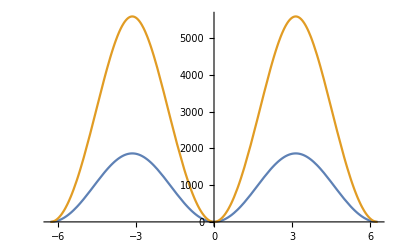

```mathematica
Plot[{getEnergy[e1,x]-getEnergy[e1,0],getEnergy[e2,x]-getEnergy[e2,0]},{x,-2π,2π}]
```

## Construct the Hamiltonian

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergy[e2,ϕa-ϕf]+getEnergy[e2,ϕb-ϕf]+getEnergy[e2,ϕc-ϕf]+getEnergy[e2,ϕd-ϕf]);
```

```mathematica
res={ϕa->0,ϕb->0,ϕc->0,ϕd->0,ϕf->0};
Monitor[
t2=Table[
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext]/.res;
{ϕext,(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[h0/.{a->1,ϕx->0.,ϕz->0,ϕw->0},{ϕy,2},0])/2,
(ND[h0/.{a->1,ϕx->0.,ϕy->0,ϕw->0},{ϕz,2},0])/2,
D[h0,ϕx,ϕy,ϕz]/.{a->1,ϕx->0,ϕy->0,ϕz->0,ϕw->0},
(*ND[ND[ND[h0/.{a->1,ϕw->0},ϕx,0],ϕy,0],ϕz,0],*)
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[ND[h0/.{a->1,ϕy->0,ϕw->0},{ϕx,2},0],{ϕz,2},0])/4,
(ND[ND[h0/.{a->1,ϕx->0,ϕw->0},{ϕy,2},0],{ϕz,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24,
(ND[h0/.{a->1,ϕx->0.,ϕz->0,ϕw->0},{ϕy,4},0])/24,
(ND[h0/.{a->1,ϕx->0.,ϕy->0,ϕw->0},{ϕz,4},0])/24}
,{ϕext,0,3π,π/10}];
,ϕext]
```

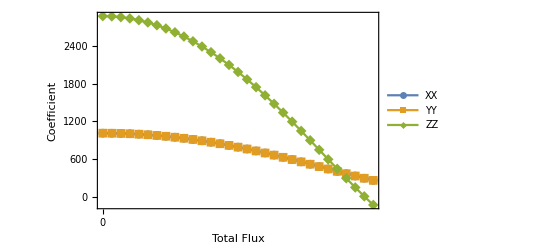

```mathematica
ListPlot[{t2[[All,{1,2}]],t2[[All,{1,3}]],t2[[All,{1,4}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"XX","YY","ZZ"}]]
```

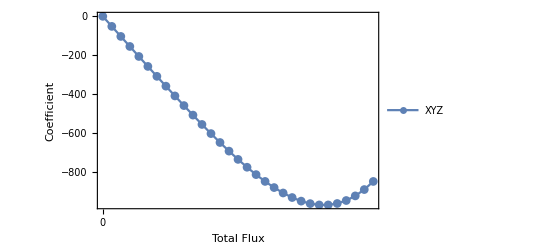

```mathematica
ListPlot[{t2[[All,{1,5}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"XYZ"}]]
```

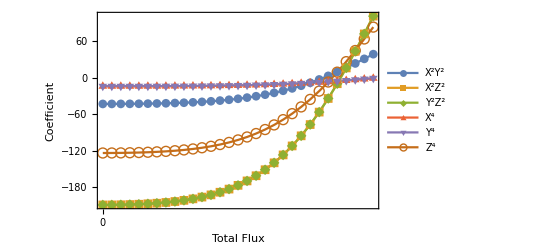

```mathematica
ListPlot[{t2[[All,{1,6}]],t2[[All,{1,7}]],t2[[All,{1,8}]],t2[[All,{1,9}]],t2[[All,{1,10}]],t2[[All,{1,11}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"X^2Y^2","X^2Z^2","Y^2Z^2","X^4","Y^4","Z^4"}]]
```

```mathematica
code=t2[[22]]
```

{(21 π)/10,591.533,591.533,1195.54,-929.242,-17.6523,-112.2,-112.2,-10.0923,-10.0923,-59.1808}

```mathematica
exp=-4 EJ β-4 EJ Cos[Subscript[φ, ex]/4]-EJ Sin[Subscript[φ, ex]/4] Subscript[φ, x] Subscript[φ, y] Subscript[φ, z]+1/4 (EJ β Subscript[φ, x]^2+2 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, x]^2+EJ β Subscript[φ, y]^2+2 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, y]^2+2 EJ β Subscript[φ, z]^2+8 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, z]^2)+1/192 (-EJ β Subscript[φ, x]^4-2 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, x]^4-12 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, x]^2 Subscript[φ, y]^2-EJ β Subscript[φ, y]^4-2 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, y]^4-6 EJ β Subscript[φ, x]^2 Subscript[φ, z]^2-48 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, x]^2 Subscript[φ, z]^2-6 EJ β Subscript[φ, y]^2 Subscript[φ, z]^2-48 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, y]^2 Subscript[φ, z]^2-2 EJ β Subscript[φ, z]^4-32 EJ Cos[Subscript[φ, ex]/4] Subscript[φ, z]^4);
```

```mathematica
Expand[N[exp/.{EJ->EJ1,β->(EJ2/EJ1),Subscript[φ, ex]->code[[1]]}]]
```

-16432.5+1006.48 φ_x^2-20.9684 φ_x^4+1006.48 φ_y^2+5.137 φ_x^2 φ_y^2-20.9684 φ_y^4-1044.35 φ_x φ_y φ_z+1930.77 φ_z^2-110.399 φ_x^2 φ_z^2-110.399 φ_y^2 φ_z^2-29.9504 φ_z^4

## Extract ps and zs

```mathematica
lj=(code[[2]]/(sf*((2*10^-15)/(2π))^2))^-1
lz=(code[[4]]/(sf*((2*10^-15)/(2π))^2))^-1
fs=7.4471*10^9;
fi=5.0847*10^9;
```

2.7261×10^-10

1.34883×10^-10

```mathematica
ress=Quiet[Solve[2π fs==1/(√((ls+lj) cs))&&√(ls/cs)==41&&ls>0]][[1]]
resi=Quiet[Solve[2π fi==1/(√((li+lj) ci))&&√(li/ci)==41&&li>0]][[1]]
```

{cs→4.46437×10^-13,ls→7.50461×10^-10}

{ci→6.86641×10^-13,li→1.15424×10^-9}

```mathematica
condition={za->√((ls+lj)/cs),zb->√((li+lj)/ci),zc->√((lz+(ls+li)/4)(1/(2 cs)+1/(2 ci))),pa->lj/(ls+lj),pb->lj/(li+lj),pc->lz/(lz+(ls+li)/4),ℏ->1.05457*10^-34,Subscript[φ, 0]->(2.0678*10^-15)/(2 π)}/.ress/.resi
```

{za→47.871,zb→45.5853,zc→33.6056,pa→0.266462,pb→0.191057,pc→0.220736,ℏ→1.05457×10^-34,φ_0→3.29101×10^-16}

## 20dB gain curve and colorplot

#### 1. Define functions

Starting from here, we solve max peak and ϵ numerically.

```mathematica
gain[κa_,κb_,g_,phoc_,m_,n_,a_,b_,Δ_,ϵ_]:=(16 g^4 phoc^4+8 g^2 phoc^2 (-4 (m phoc^2+Δ) (b+n phoc^2-Δ+ϵ)+κa κb)+4 a^2 (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+(4 (m phoc^2+Δ)^2+κa^2) (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+8 a (4 (b+n phoc^2-Δ+ϵ) (-g^2 phoc^2+(m phoc^2+Δ) (b+n phoc^2-Δ+ϵ))+(m phoc^2+Δ) κb^2))/(16 g^4 phoc^4+8 g^2 phoc^2 (-4 (m phoc^2+Δ) (b+n phoc^2-Δ+ϵ)-κa κb)+4 a^2 (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+(4 (m phoc^2+Δ)^2+κa^2) (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+8 a (4 (b+n phoc^2-Δ+ϵ) (-g^2 phoc^2+(m phoc^2+Δ) (b+n phoc^2-Δ+ϵ))+(m phoc^2+Δ) κb^2)); (* this is the function of gain from Rgain2 *)
computeΔmax[κa_,κb_,g_,phoc_,m_,n_,a_,b_,ϵ_]:=1/2 (-a+b-m phoc^2+n phoc^2+ϵ)+(-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)/(12 2^(2/3) (-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2+√(4 (-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)^3+(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2)^2))^(1/3))-1/(24 2^(1/3))(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2+√(4 (-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)^3+(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2)^2))^(1/3);  (* this is the function for max peak *) 
maxGain[κa_,κb_,g_,phoc_,m_,n_,a_,b_,ϵ_]:=Module[{Δmax}, 
Δmax=computeΔmax[κa,κb,g,phoc,m,n,a,b,ϵ];
Return[gain[κa,κb,g,phoc,m,n,a,b,Δmax,ϵ]];
];  (* This function return the value of gain when Δ=Δmax *)
Gvsϵ[κa_,κb_,g_,GG_,m_,n_,a_,b_,ϵ_,phoc0_]:=Module[{phoc,res},
res=FindRoot[maxGain[κa,κb,g,phoc,m,n,a,b,ϵ]==GG,{phoc,phoc0}];
Return[phoc/.res];
];(* This function return phoc with given pump power *)
```

#### 2. Give parameters

```mathematica
(* Give parameters *)
κa=2 π 0.06217;κb=2 π 0.02027;GG=100;
g=2π code[[5]](pa pb pc ℏ √(za zb zc ℏ))/(2 √2 Subscript[φ, 0]^3)/.condition;αα=-2π code[[9]](ℏ^2 pa^4 za^2)/(4 Subscript[φ, 0]^4)/.condition;ββ=-2π code[[10]](ℏ^2 pb^4 zb^2)/(4 Subscript[φ, 0]^4)/.condition;γγ=-2π code[[11]](ℏ^2 pc^4 zc^2)/(4 Subscript[φ, 0]^4)/.condition;δδ=-2π code[[6]](ℏ^2 pa^2 pb^2 za zb)/(4 Subscript[φ, 0]^4)/.condition;λλ=-2π code[[7]](ℏ^2 pa^2 pc^2 za zc)/(4 Subscript[φ, 0]^4)/.condition;ϵϵ=-2π code[[8]](ℏ^2 pb^2 pc^2 zb zc)/(4 Subscript[φ, 0]^4)/.condition;
a=(12αα+2δδ+2λλ);
b=(12ββ+2δδ+2ϵϵ);m=4λλ;n=4λλ;l=4δδ;
Print[{"g=  ",g/(2π)},{"Kaa=  ",αα/(2π)},{"Kbb=  ",ββ/(2π)},{"Kcc=  ",γγ/(2π)},{"Kab=  ",δδ/(2π)},{"Kac=  ",λλ/(2π)},{"Kbc=  ",ϵϵ/(2π)}]
```

{g=  ,-0.0303764}{Kaa=  ,0.0000276348}{Kbb=  ,6.62315×10^-6}{Kcc=  ,0.0000376072}{Kab=  ,0.000023663}{Kac=  ,0.000148003}{Kbc=  ,0.0000724559}

#### 3. Calculate 20dB gain phoc and Δmax

```mathematica
(* Here, we sweep ϵ and find the coresponding phoc*)
ϵmax=2π 0.02;ϵmin=-2 π 0.02;ϵstep=2 π 0.001;
ϵnumber=(ϵmax-ϵmin)/ϵstep+1;
ϵarray=Table[i,{i,ϵmin, ϵmax,ϵstep}];
Monitor[
t2=Table[
t1=Table[
Quiet[Gvsϵ[κa,κb,g,GG,m,n,a,b,ϵ,phoc0]]
,{phoc0,0.0001,2,0.1}];
Flatten[{ϵ,Union[Abs[t1], SameTest->(Abs[#1-#2]<10^-4&)]}]
,{ϵ,ϵmin, ϵmax,ϵstep}];
,ϵ/(2π)]
tt=Table[{t2[[i,1]]/(2 π),10*Log10[1/0.001 t2[[i,2]]^2*1.05457*^-34*2 π 22.544*10^9*2π 1456.69*10^9]},{i,1,ϵnumber}];
```

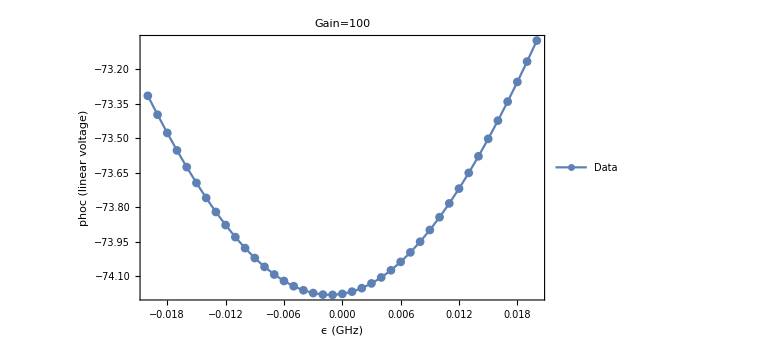

```mathematica
ListPlot[tt, Frame->True,ImageSize->Large, FrameLabel->{"ϵ (GHz)","phoc (linear voltage)"}, FrameStyle->Directive[Thick,14], PlotLabel->"Gain=100", Joined->True, PlotMarkers->Automatic,PlotLegends->LineLegend[{"Data","Parabola","Hyperbola"}]]
```

```mathematica
Export[NotebookDirectory[]<>"20 dB gain.csv",tt,"CSV","CompressionLevel"->0] ;
```

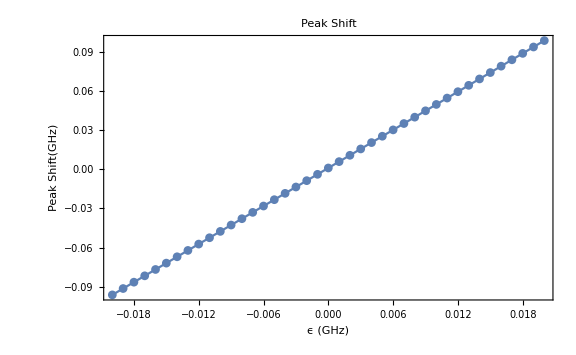

```mathematica
(* Peak of 20dB Gain vs ϵ *)
t3=Table[
{t2[[i,1]]/(2 π),computeΔmax[κa,κb,g,t2[[i,2]],m,n,a,b,t2[[i,1]]]},
{i,Length[t2]}];
ListPlot[t3, Frame->True, ImageSize->Large,FrameLabel->{"ϵ (GHz)","Peak Shift(GHz)"}, FrameStyle->Directive[Thick,14], PlotLabel->"Peak Shift", Joined->True, PlotMarkers->Automatic]
```

```mathematica
(* Here, we just want to prove that peak of gain is leaded by ϵ/2-(n-m)/2 phoc^2 *)
t4=Table[
{computeΔmax[κa,κb,g,t2[[i,2]],m,n,a,b,t2[[i,1]]]-( t2[[i,1]]/2)}
,{i,Length[t2]}]
```

{{-0.0333655},{-0.0316422},{-0.0299205},{-0.0282002},{-0.0264813},{-0.0247638},{-0.0230474},{-0.0213322},{-0.0196181},{-0.0179048},{-0.0161923},{-0.0144805},{-0.0127692},{-0.0110583},{-0.00934756},{-0.00763692},{-0.00592618},{-0.00421519},{-0.00250378},{-0.000791775},{0.000920992},{0.00263469},{0.00434949},{0.00606557},{0.00778307},{0.00950218},{0.011223},{0.0129458},{0.0146706},{0.0163977},{0.018127},{0.0198588},{0.0215932},{0.0233303},{0.0250702},{0.0268129},{0.0285586},{0.0303074},{0.0320592},{0.0338143},{0.0355725}}

### 6. Define functions for calculation of α/β

#### 1. Define useful functions

```mathematica
getαβ[phoc_?NumberQ]:=Module[{res},
res=Reduce[Rationalize[
{(κa/2-ⅈ(Δ+a+m phoc^2+12 αα/κa(1+α)(1+Conjugate[α]) phoa^2+l/κb β Conjugate[β] phoa^2))(1+α)/(√κa)==-ⅈ (g phoc)/(√κb)β+√κa,
(κb/2-ⅈ(-Δ+ϵ+b+n phoc^2+12 ββ/κb β Conjugate[β] phoa^2+l/κa(1+α)(1+Conjugate[α]) phoa^2))Conjugate[β]/(√κb)==-ⅈ (g phoc)/(√κa)(1+Conjugate[α])
}]
,{α,β}];
Return[
If[Length[res]==2,
Flatten[Table[res[[i,2]],{i,2}]],
Flatten[Table[Table[res[[i,j,2]],{j,Length[res[[i]]]}],{i,Length[res]}]]]
];
];
Off[Reduce::ratnz];
```

#### 2. Calculation of α and β (required result from 1.3 )

```mathematica
Clear[α,β];
constant=2π 0.06217*10^9*2 π 7.4471*^9*1.05457*^-34;

(*phoamin=0.0170*0;phoamax=0.005*200;phoastep=0.01;
phoanumber=(phoamax-phoamin)/phoastep+1;
naarray=Table[i,{i,phoamin,phoamax,phoastep}];
phoadb=Table[10Log10[(i^2*constant)/0.001],{i,phoamin,phoamax,phoastep}];*)

phoadb=Table[i,{i,-158,-128,1}];
naarray=Table[√(0.001/constant 10^(0.1*phoadb[[i]])),{i,1,Length[phoadb]}];
```

```mathematica
resreduce=
Monitor[
Table[
Table[
ϵ=t2[[x,1]];
Δ=t3[[x,2]];
phoc=t2[[x,2]];
phoa=naarray[[y]];
getαβ[phoc]
,{y,1,Length[naarray]}]
,{x,1,ϵnumber}]
,{x,ProgressIndicator[x,{1,ϵnumber}],y,ProgressIndicator[y,{1,Length[naarray]}]}];
```

#### 3. Obtaining the right α and β

```mathematica
αarray=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}]; 
βarray=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}];
For[x=1,x≤ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
t=Table[20Log10[Abs[resreduce[[x,y,i]]]],{i,1,Length[resreduce[[x,y]]],2}];
hahaha=resreduce[[x,y,2*Flatten[Position[t,Min[t]]]-1]];
αarray[[x,y]]=hahaha[[1]];
h=Table[20Log10[Abs[resreduce[[x,y,i]]]],{i,2,Length[resreduce[[x,y]]],2}];
haha=resreduce[[x,y,2*Flatten[Position[t,Min[t]]]]];
βarray[[x,y]]=haha[[1]];
];
]
```

#### 4. Plot Mag of α and β

```mathematica
drresultα=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}];
drresultβ=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}];
drdataα=Table[0,{i,1,ϵnumber}];
drdataβ=Table[0,{i,1,ϵnumber}];
```

```mathematica
For[x=1,x≤ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
drresultα[[x,y]]=20Log10[Abs[αarray[[x,y]]]];
drresultβ[[x,y]]=20Log10[Abs[βarray[[x,y]]]];
];
drdataα[[x]]=Transpose@{phoadb,drresultα[[x]]};
drdataβ[[x]]=Transpose@{phoadb,drresultβ[[x]]};
]
```

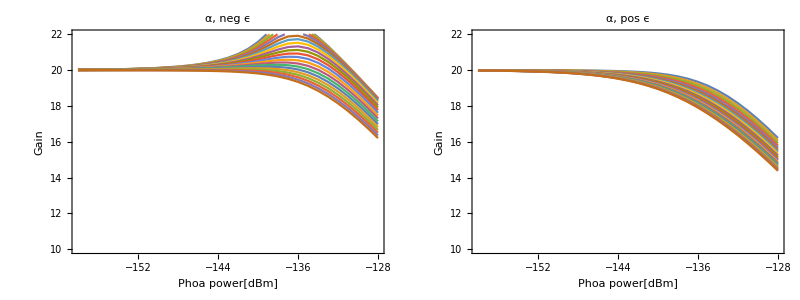

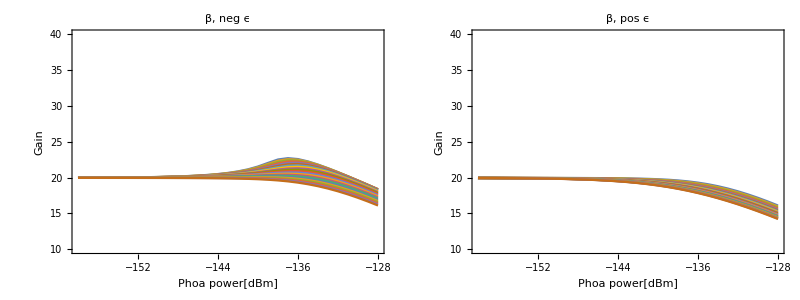

```mathematica
negϵmagdataα=Table[drdataα[[i]],{i,1,(Ceiling[ϵnumber]-1)/2+1}];
posϵmagdataα=Table[drdataα[[i]],{i,(Ceiling[ϵnumber]-1)/2+1,Ceiling[ϵnumber]}];
negϵmagdataβ=Table[drdataβ[[i]],{i,1,(Ceiling[ϵnumber]-1)/2+1}];
posϵmagdataβ=Table[drdataβ[[i]],{i,(Ceiling[ϵnumber]-1)/2+1,Ceiling[ϵnumber]}];
p1=ListPlot[negϵmagdataα,ImageSize->Large,Joined->True,PlotRange->{All,{10,22}},Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Gain"},PlotLabel->"α, neg ϵ"];
p2=ListPlot[posϵmagdataα,ImageSize->Large,Joined->True,PlotRange->{All,{10,22}},Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Gain"},PlotLabel->"α, pos ϵ"];
p3=ListPlot[negϵmagdataβ,ImageSize->Large,Joined->True,PlotRange->{10,40},Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Gain"},PlotLabel->"β, neg ϵ"];
p4=ListPlot[posϵmagdataβ,ImageSize->Large,Joined->True,PlotRange->{10,40},Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Gain"},PlotLabel->"β, pos ϵ"];
Grid[{{p1,p2}}]
Grid[{{p3,p4}}]
```

```mathematica
colordataα=Table[{0,0,i},{i,1,ϵnumber*Length[naarray]}];
n=0;
For[x=1,x<=ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
colordataα[[n*Length[naarray]+y,1]]=ϵarray[[x]]/(2 π);
colordataα[[n*Length[naarray]+y,2]]=phoadb[[y]];
colordataα[[n*Length[naarray]+y,3]]=drresultα[[x,y]];
];
n=n+1;
]
colordataβ=Table[{0,0,i},{i,1,ϵnumber*Length[naarray]}];
n=0;
For[x=1,x<=ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
colordataβ[[n*Length[naarray]+y,1]]=ϵarray[[x]]/(2 π);
colordataβ[[n*Length[naarray]+y,2]]=phoadb[[y]];
colordataβ[[n*Length[naarray]+y,3]]=drresultβ[[x,y]];
];
n=n+1;
]
```

```mathematica
c1=ListDensityPlot[colordataα,ImageSize->{72*3.37,72*3.37},PlotRange->All,ColorFunction->Setting@ColorData["TemperatureMap"],FrameLabel->{"Pump detuning (GHz)","Signal power(dBm)"},LabelStyle->Directive[Black,FontSize->10],
Mesh->8,MeshFunctions->{Boole[Greater[#3,21]]&,Boole[Greater[#3,19]]&},MeshStyle->{Directive[Red],Directive[Black]},
PlotLegends->{Placed[
BarLegend[
{Setting@ColorData["TemperatureMap"],{14,25}},LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{10,180},LegendLabel->Placed["Gain (dB)",Right,Rotate[#,90 Degree]&]
],
{{1.3,0.5},{1.2,0.47}}
]}
];
rText=Text[Style["- P+1 dB",FontSize->8,Red],{0.007,-135}];
bText=Text[Style["- P-1 dB",FontSize->8,Black],{0.007,-140}];
txt=Graphics[{rText,bText}];
c1=Show[c1,txt]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"colorplot reflection_v2.csv",colordataα,"CSV","CompressionLevel"->0]
```

E:\BoxSync\TZC\Theory Projects\JPCs gain\20161213 till Now - Fig for paper\20170717 wtf\colorplot reflection_v2.csv

```mathematica
c2=ListDensityPlot[colordataβ,ImageSize->{72*3.37,72*3.37},PlotRange->All,ColorFunction->Setting@ColorData["TemperatureMap"],FrameLabel->{"Pump detuning (GHz)","Signal power(dBm)"},LabelStyle->Directive[Black,FontSize->10],
Mesh->8,MeshFunctions->{Boole[Greater[#3,21]]&,Boole[Greater[#3,19]]&},MeshStyle->{Directive[Red],Directive[Black]},
PlotLegends->{Placed[
BarLegend[
{Setting@ColorData["TemperatureMap"],{14,25}},LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{10,180},LegendLabel->Placed["Gain (dB)",Right,Rotate[#,90 Degree]&]
],
{{1.3,0.5},{1.2,0.47}}
]}
];
rText=Text[Style["- P+1 dB",FontSize->8,Red],{0.01,-125}];
bText=Text[Style["- P-1 dB",FontSize->8,Black],{0.01,-130}];
txt=Graphics[{rText,bText}];
c2=Show[c2,txt]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"colorplot transmission_v2.csv",colordataβ,"CSV","CompressionLevel"->0]
```

E:\BoxSync\TZC\Theory Projects\JPCs gain\20161213 till Now - Fig for paper\20170717 wtf\colorplot transmission_v2.csv

#### 5. Plot Phase of α and β

```mathematica
phdrresultα=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}];
phdrresultβ=Table[
Table[0,{i,1,Length[naarray]}]
,{i,1,ϵnumber}];
phdataα=Table[0,{i,1,ϵnumber}];
phdataβ=Table[0,{i,1,ϵnumber}];
phase[vec_List]:=Module[{phi,df,len,i},phi=Arg@vec;
df=Differences@phi;
len=Length@phi;
i=Flatten@Position[df,x_/;Abs[x]>3.5];
Do[phi=phi-(2 Pi*Sign[df[[j]]]*UnitStep[#-(j+1)]&/@Range[len]),{j,i}];
phi]
```

```mathematica
For[x=1,x≤ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
t=Table[20Log10[Abs[resreduce[[x,y,i]]]],{i,1,Length[resreduce[[x,y]]],2}];
hahaha=resreduce[[x,y,2*Flatten[Position[t,Min[t]]]-1]];
phdrresultα[[x,y]]=180/π*phase[hahaha][[1]];
h=Table[20Log10[Abs[resreduce[[x,y,i]]]],{i,2,Length[resreduce[[x,y]]],2}];
haha=resreduce[[x,y,2*Flatten[Position[t,Min[t]]]]];
phdrresultβ[[x,y]]=180/π*phase[haha][[1]];
];
phdrresultα[[x]]=phdrresultα[[x]]-phdrresultα[[x,1]];
phdrresultβ[[x]]=phdrresultβ[[x]]-phdrresultβ[[x,1]];
phdataα[[x]]=Transpose@{phoadb,phdrresultα[[x]]};
phdataβ[[x]]=Transpose@{phoadb,phdrresultβ[[x]]};
]
```

```mathematica
For[x=1,x≤ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
phdataα[[x,y,2]]=phdataα[[x,y,2]]-phdataα[[x,1,2]];
phdataβ[[x,y,2]]=phdataβ[[x,y,2]]-phdataβ[[x,1,2]];
];
]
```

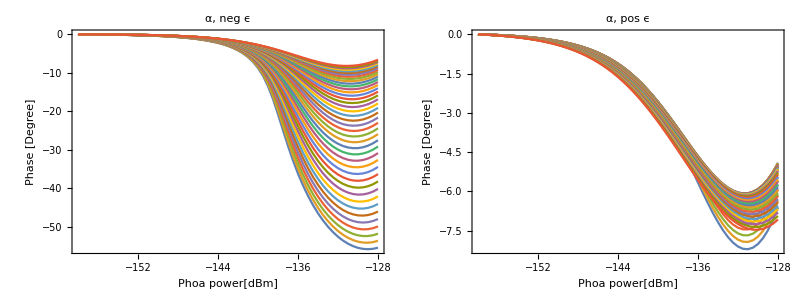

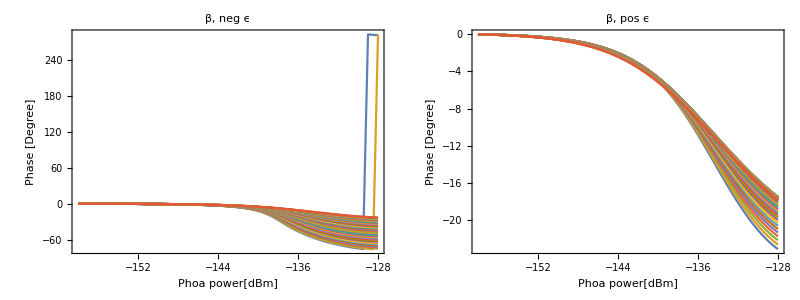

```mathematica
negϵphsdataα=Table[phdataα[[i]],{i,1,(ϵnumber-1)/2+1}];
posϵphsdataα=Table[phdataα[[i]],{i,(ϵnumber-1)/2+1,ϵnumber}];
negϵphsdataβ=Table[phdataβ[[i]],{i,1,(ϵnumber-1)/2+1}];
posϵphsdataβ=Table[phdataβ[[i]],{i,(ϵnumber-1)/2+1,ϵnumber}];
p5=ListPlot[negϵphsdataα,ImageSize->Large,Joined->True,PlotRange->All,Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Phase [Degree]"},PlotLabel->"α, neg ϵ"];
p6=ListPlot[posϵphsdataα,ImageSize->Large,Joined->True,PlotRange->All,Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Phase [Degree]"},PlotLabel->"α, pos ϵ"];
p7=ListPlot[negϵphsdataβ,ImageSize->Large,Joined->True,PlotRange->All,Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Phase [Degree]"},PlotLabel->"β, neg ϵ"];
p8=ListPlot[posϵphsdataβ,ImageSize->Large,Joined->True,PlotRange->All,Frame->True, FrameStyle->Directive[Thick,16],FrameLabel->{"Phoa power[dBm]","Phase [Degree]"},PlotLabel->"β, pos ϵ"];
Grid[{{p5,p6}}]
Grid[{{p7,p8}}]
```

```mathematica
phcolordataα=Table[{0,0,i},{i,1,ϵnumber*Length[naarray]}];
```

```mathematica
n=0;
For[x=1,x<=ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
phcolordataα[[n*Length[naarray]+y,1]]=ϵarray[[x]];
phcolordataα[[n*Length[naarray]+y,2]]=phoadb[[y]];
phcolordataα[[n*Length[naarray]+y,3]]=-1*phdrresultα[[x,y]];
];
n=n+1;
];
phcolordataβ=Table[{0,0,i},{i,1,ϵnumber*Length[naarray]}];
n=0;
For[x=1,x<=ϵnumber,x++,
For[y=1,y≤Length[naarray],y++,
phcolordataβ[[n*Length[naarray]+y,1]]=ϵarray[[x]];
phcolordataβ[[n*Length[naarray]+y,2]]=phoadb[[y]];
phcolordataβ[[n*Length[naarray]+y,3]]=-1*phdrresultβ[[x,y]];
];
n=n+1;
]
```

```mathematica
test=Table[i,{i,1,Length[ϵarray]},{j,1,Length[phoadb]}];
```

```mathematica
For[i=1,i≤Length[ϵarray],i++,
For[j=1,j≤Length[phoadb],j++,
test[[i,j]]=-1*phdrresultβ[[i,j]]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"transmission phase_v4.csv",test,"CSV","CompressionLevel"->0] ;
```

```mathematica
c3=ListDensityPlot[phcolordataα,ImageSize->{72*3.37,72*3.37},PlotRange->All,ColorFunction->Setting@ColorData["TemperatureMap"],FrameLabel->{"Pump detuning (2 π GHz)","Signal power(dBm)"},LabelStyle->Directive[Black,FontSize->10],
PlotLegends->{Placed[
BarLegend[
{Setting@ColorData["TemperatureMap"],{-5,20}},LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{10,180},LegendLabel->Placed["Phase (Degree)",Right,Rotate[#,90 Degree]&]
],
{{1.35,0.5},{1.2,0.47}}
]}
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"color plot phase α.emf",c3,"EMF","CompressionLevel"->0,ImageSize->{72*3.37,72*3.37}] (*export the graph*)
```

E:\BoxSync\TZC\Theory Projects\JPC's gain\20161213 till Now - Fig for paper\20170131  matching theory with data\color plot phase α.emf

```mathematica
c4=ListDensityPlot[phcolordataβ,ImageSize->{72*3.37,72*3.37},PlotRange->All,ColorFunction->Setting@ColorData["TemperatureMap"],FrameLabel->{"Pump detuning (2 π GHz)","Signal power(dBm)"},LabelStyle->Directive[Black,FontSize->10],
PlotLegends->{Placed[
BarLegend[
{Setting@ColorData["TemperatureMap"],{-5,20}},LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{10,180},LegendLabel->Placed["Phase (Degree)",Right,Rotate[#,90 Degree]&]
],
{{1.35,0.5},{1.2,0.47}}
]}
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"color plot phase β.emf",c4,"EMF","CompressionLevel"->0] (*export the graph*)
```

E:\BoxSync\TZC\Theory Projects\JPC's gain\20161213 till Now - Fig for paper\20170131  matching theory with data\color plot phase β.emf

### 7. 20dB gain for a given phoa

#### 1. Define useful functions

```mathematica
(*
This function computes α, β and phoc that are required to get |α|^2=amp; The function returns {α1,α2,β1,β2,phoc} quintuplet for each solution that it find
*)
findPhoCR[κa_?NumberQ,κb_?NumberQ,a_?NumberQ,b_?NumberQ,m_?NumberQ,n_?NumberQ,l_?NumberQ,g_?NumberQ,phoa_?NumberQ,Δ_?NumberQ,ϵ_?NumberQ,GG_?NumberQ]:=Module[{res,α1,α2, β1,β2, phoc},
res=Reduce[
{1/(2 κa^(3/2) κb)(2 l phoa^2 α2 (β1^2+β2^2) κa+24 phoa^2 α2 (1+2 α1+α1^2+α2^2) αα κb+2 a α2 κa κb+2 m phoc^2 α2 κa κb+2 α2 Δ κa κb-κa^2 κb+α1 κa^2 κb-2 g phoc β2 √(κa^3 κb))==0.,
1/(2 κa^(3/2) κb)(-2 l phoa^2 (1+α1) (β1^2+β2^2) κa-24 phoa^2 (1+α1) (1+2 α1+α1^2+α2^2) αα κb-2 a κa κb-2 m phoc^2 κa κb-2 a α1 κa κb-2 m phoc^2 α1 κa κb-2 Δ κa κb-2 α1 Δ κa κb+α2 κa^2 κb+2 g phoc β1 √(κa^3 κb))==0.,
1/(2 κa κb^(3/2))(-2 b β2 κa κb-2 n phoc^2 β2 κa κb+2 β2 Δ κa κb-2 β2 ϵ κa κb+β1 κa κb^2+2 g phoc α2 √(κa κb^3)-2 phoa^2 β2 (12 β1^2 ββ κa+12 β2^2 ββ κa+l (1+2 α1+α1^2+α2^2) κb))==0.,
1/(2 κa κb^(3/2))(-2 b β1 κa κb-2 n phoc^2 β1 κa κb+2 β1 Δ κa κb-2 β1 ϵ κa κb-β2 κa κb^2+2 g phoc √(κa κb^3)+2 g phoc α1 √(κa κb^3)-2 phoa^2 β1 (12 β1^2 ββ κa+12 β2^2 ββ κa+l (1+2 α1+α1^2+α2^2) κb))==0.,
α1^2+α2^2==GG}
,{α1,α2,β1,β2,phoc},Reals];
Return[
Table[
Table[
res[[i,j,2]]
,{j,Length[res[[i]]]}]
,{i,Length[res]}]
];
];
Off[Reduce::ratnz];
(*
This function computes α, β and phoc that are required to get |α|^2=amp; The function returns {α1,α2,β1,β2,phoc} quintuplet for each solution that it find
*)
findPhoCfd[κa_?NumberQ,κb_?NumberQ,a_?NumberQ,b_?NumberQ,m_?NumberQ,n_?NumberQ,l_?NumberQ,g_?NumberQ,phoa_?NumberQ,Δ_?NumberQ,ϵ_?NumberQ,GG_?NumberQ,α10_,α20_,β10_,β20_,phoc0_]:=Module[{res,α1,α2, β1,β2, phoc},
res=FindRoot[
{1/(2 κa^(3/2) κb)(2 l phoa^2 α2 (β1^2+β2^2) κa+24 phoa^2 α2 (1+2 α1+α1^2+α2^2) αα κb+2 a α2 κa κb+2 m phoc^2 α2 κa κb+2 α2 Δ κa κb-κa^2 κb+α1 κa^2 κb-2 g phoc β2 √(κa^3 κb))==0.,
1/(2 κa^(3/2) κb)(-2 l phoa^2 (1+α1) (β1^2+β2^2) κa-24 phoa^2 (1+α1) (1+2 α1+α1^2+α2^2) αα κb-2 a κa κb-2 m phoc^2 κa κb-2 a α1 κa κb-2 m phoc^2 α1 κa κb-2 Δ κa κb-2 α1 Δ κa κb+α2 κa^2 κb+2 g phoc β1 √(κa^3 κb))==0.,
1/(2 κa κb^(3/2))(-2 b β2 κa κb-2 n phoc^2 β2 κa κb+2 β2 Δ κa κb-2 β2 ϵ κa κb+β1 κa κb^2+2 g phoc α2 √(κa κb^3)-2 phoa^2 β2 (12 β1^2 ββ κa+12 β2^2 ββ κa+l (1+2 α1+α1^2+α2^2) κb))==0.,
1/(2 κa κb^(3/2))(-2 b β1 κa κb-2 n phoc^2 β1 κa κb+2 β1 Δ κa κb-2 β1 ϵ κa κb-β2 κa κb^2+2 g phoc √(κa κb^3)+2 g phoc α1 √(κa κb^3)-2 phoa^2 β1 (12 β1^2 ββ κa+12 β2^2 ββ κa+l (1+2 α1+α1^2+α2^2) κb))==0.,
α1^2+α2^2==GG}
,{{α1,α10},{α2,α20},{β1,β10},{β2,β20},{phoc,phoc0}},MaxIterations->∞];

Return[{α1,α2,β1,β2,phoc}/.res];
];
```

#### 2. Find 20dB curve for a given phoa range _ findroot (required result from 1.3)

```mathematica
constant=2π 0.06217*10^9*2 π 7.4471*^9*1.05457*^-34;
phoadb=Table[i,{i,-158,-128,1}];
phoaarray=Table[√(0.001/constant 10^(0.1*phoadb[[i]])),{i,1,Length[phoadb]}]; 
phoanumber=Length[phoadb];
alldata=Table[0,{i,1,phoanumber}];
αβdata=Table[0,{i,1,phoanumber}];
phocarray=Table[0,{i,1,ϵnumber}];
tempαβphoc=Table[0,{i,1,ϵnumber}];
```

```mathematica
For[y=1,y≤phoanumber,y++,
PrintTemporary[y];
phoa=phoaarray[[y]];
If[y==1,
For[x=1,x≤ϵnumber,x++,
ϵ=t2[[x,1]];
Δ=t3[[x,2]];
tempresult=findPhoCR[κa,κb,a,b,m,n,l,g,phoa,Δ,ϵ,GG];
t=Table[tempresult[[i,5]],{i,1,Length[tempresult]}];
phocarray[[x]]={ϵarray[[x]]/(2π),Min[Select[t,#>0&]]};
h=Position[tempresult,Min[Select[t,#>0&]]][[1,1]];
tempαβphoc[[x]]=tempresult[[h]]
];
alldata[[y]]=phocarray;, 

For[x=1,x≤ϵnumber,x++,
ϵ=t2[[x,1]];
Δ=t3[[x,2]];
tempresult=Quiet[findPhoCfd[κa,κb,a,b,m,n,l,g,phoa,Δ,ϵ,GG,tempαβphoc[[x,1]],tempαβphoc[[x,2]],tempαβphoc[[x,3]],tempαβphoc[[x,4]],tempαβphoc[[x,5]]]];
phocarray[[x]]={ϵarray[[x]]/(2π),tempresult[[5]]};
tempαβphoc[[x]]=tempresult;
];
alldata[[y]]=phocarray;
]
]
```

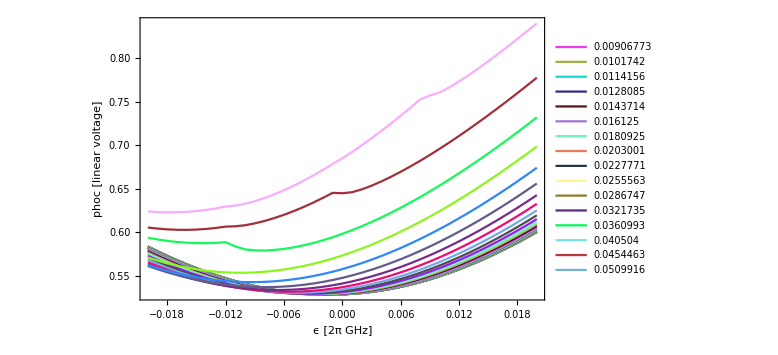

```mathematica
Show[Table[ListPlot[{alldata[[i,All,{1,2}]]},ImageSize->Large,Joined->True,Frame->True, PlotLegends->{phoaarray[[i]]},FrameStyle->Directive[Thick,16],FrameLabel->{"ϵ [2π GHz]","phoc [linear voltage]"},PlotStyle->{RandomColor[i]}],{i,Length[alldata]}],PlotRange->All]
```

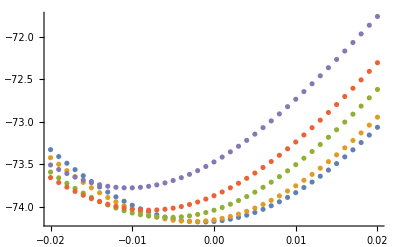

-131

```mathematica
h=28;
temp131=Table[
{alldata[[h,i,1]],10*Log10[1/0.001 alldata[[h,i,2]]^2*1.05457*^-34*2 π 22.544*10^9*2π 1456.69*10^9]}
,{i,Length[alldata[[h]]]}];
ListPlot[{temp150,temp140,temp135,temp133,temp131}]
phoadb[[h]]
```

```mathematica
Export[NotebookDirectory[]<>"gain131.csv",temp131[[All,2]],"CSV","CompressionLevel"->0] ;
```